# Pathfinding w/ A* Robert Aburustum

## Algorithms

### Depth First Search* Breadth First Search* Best-First Search Dijkstra’s Algorithm* A* * = already in Mathematica

## A* Implementation

```mathematica
(*TODO
*Lights out style manipulation - clicked nodes change color to indicate blocked
*try other heuristics for the cost function - look at other people's algorithms
*add go back function to show optimal path
*sliders for size (height & width)
*options for 3d/2d/both
*Keep in contact with Christian/Rob/others
*make it easier to see closed nodes vs open nodes vs untouched nodes
*)
```

## Testing

### Start/Goal Node Initialization

```mathematica
startNodeCoords = {1.,1.}; 
goalNodeCoords = {10.,10.};
```

### Graph Generation

```mathematica
Clear[graph]
```

```mathematica
baseGraph = GridGraph[{10,10}];
baseNodeList = VertexList[baseGraph];
baseNodeCoordList = GraphEmbedding[baseGraph];
meanPt=Mean[baseNodeCoordList];
```

### Covered Node Generation

```mathematica
diskPosList = {3,3};
getCoveredNodes[diskPosList_]:=Alternatives@@Flatten[Position[baseNodeCoordList,p_/;Norm[p-diskPosList]≤1,{1}]]
covered=getCoveredNodes[diskPosList](*Mark for later replacement with random disk coordinates*)
getCoveredNodeCoords[diskPosList_]:= getCoords/@ getCoveredNodes[diskPosList]
coveredNodeCoords=getCoveredNodeCoords[{3,3}]
```

13|22|23|24|33

{2.,3.}|{3.,2.}|{3.,3.}|{3.,4.}|{4.,3.}

```mathematica
Show[Graph@Cases[EdgeList[baseGraph],_?(FreeQ[covered])], Graphics[Disk[meanPt]]]; (*OLD*)
```

### genGraph

```mathematica
genGraph[covered_] := Graph@Cases[EdgeList[GridGraph[{10,10}]],_?(FreeQ[covered])]
```

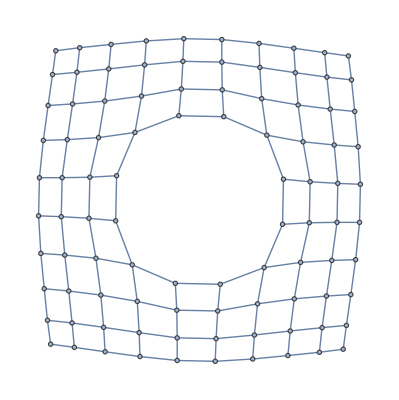

```mathematica
graph = genGraph[covered]
```

### genGraphV2

```mathematica
genGraphV2[coveredNodes_, coveredNodeCoords_]:=Graph[VertexDelete[baseGraph,coveredNodes],VertexCoordinates ->DeleteCases[baseNodeCoordList[[1;;]], x_/;!FreeQ[x,coveredNodeCoords]]]
```

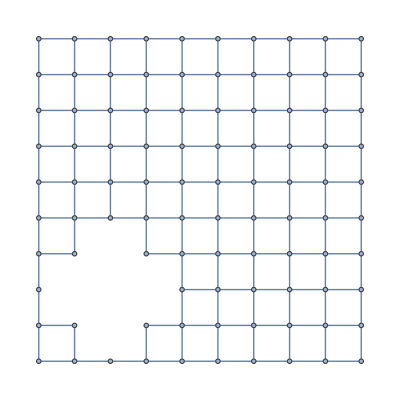

```mathematica
graph = genGraphV2[covered, coveredNodeCoords]
```

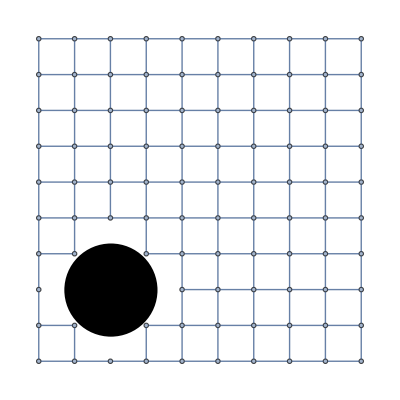

```mathematica
visualGraph = Show[graph, Graphics[{Disk[{3,3},1.3]}]] (*WIP - V3 could add diagonal edges around the disks to make a more realistic obstacle - be sure to reenable diagonals as succesors if this is done - final version of visualgraph / graph should generate the disks from coordinates given by random point gens or from user input manipulate*)
```

### genGraphV3

```mathematica
testGetSuccessorNodes[n_]:= With[{nodeCoord=getCoords[n]//Flatten}, DeleteCases[{nodeCoord+{1,0}, nodeCoord-{1,0}, nodeCoord+{0,1}, nodeCoord-{0,1}, nodeCoord+{1,1}, nodeCoord-{1,1}, nodeCoord+{1,-1}, nodeCoord+{-1,1}}, x_/;FreeQ[GraphEmbedding[graph], x]]]
```

```mathematica
testGetSuccessorNodes[3]
```

{{2.,3.},{1.,4.},{1.,2.},{2.,4.},{2.,2.}}

```mathematica
genGraphV3[coveredNodes_, coveredNodeCoords_]:=Graph[Graph[VertexDelete[baseGraph,coveredNodes],VertexCoordinates ->DeleteCases[baseNodeCoordList[[1;;]], x_/;!FreeQ[x,coveredNodeCoords]]],]
```

```mathematica
graph = genGraphV3[covered, coveredNodeCoords];
```

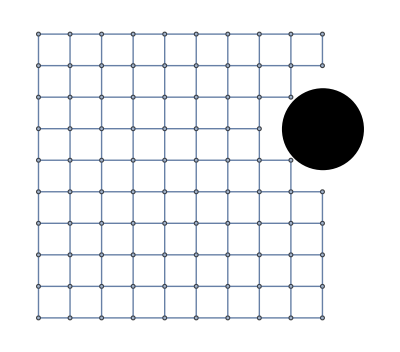

```mathematica
visualGraph = Show[graph, Graphics[{Disk[diskPosList,1.3]}]] (*WIP - V3 could add diagonal edges around the disks to make a more realistic obstacle - be sure to reenable diagonals as succesors if this is done - final version of visualgraph / graph should generate the disks from coordinates given by random point gens or from user input manipulate*)
```

### Node List Initialization

```mathematica
openNodes ={ {startNodeCoords},{0}};
closedNodes = {};
```

### Cost Function Definition

```mathematica
distFromSNode[n_] := Floor[Total[ n-startNodeCoords]/5](*The distance in edges from the start node to the given node 'n'*)

heuristic[n_] :=SquaredEuclideanDistance[n,goalNodeCoords] (*Squared Euclidian distance between the goal node and the given node 'n'*)

cost[n_]:=If[{1.,1.}==n,Return[0], distFromSNode[n]^2 + heuristic[n]] (*Cost of a given node 'n'*)
```

```mathematica
runningCost[cn_,pn_]:=N[(Floor[Total[ n-startNodeCoords]]+EuclideanDistance[cn,pn])^2]
```

### Node successor generation definition

```mathematica
getCoords[n_]:= Return[GraphEmbedding[baseGraph][[n]]]
```

```mathematica
genSuccsessorNodes[n_]:= Module[{nodeCoord=getCoords[n]//Flatten}, DeleteCases[{nodeCoord+{1,0}, nodeCoord-{1,0}, nodeCoord+{0,1}, nodeCoord-{0,1}(*, nodeCoord+{1,1}, nodeCoord-{1,1}, nodeCoord+{1,-1}, nodeCoord+{-1,1}*)}, x_/;FreeQ[GraphEmbedding[graph], x]]]
```

```mathematica
(*Uncomment above to allow for diagonal nodes to be recognized as valid successors - the above function also automatically checks to be sure the successor is not already in the open list*)
```

```mathematica
genSuccsessorNodes[57]
```

{{7.,7.},{5.,7.},{6.,8.},{6.,6.}}

### Not a Bug w/ VertexDelete but a cool way around an annoying function implementation

```mathematica
bugFixGraph = GridGraph[{5,5}];
bugGraphCoords = GraphEmbedding[bugFixGraph]
```

{{1.,1.},{1.,2.},{1.,3.},{1.,4.},{1.,5.},{2.,1.},{2.,2.},{2.,3.},{2.,4.},{2.,5.},{3.,1.},{3.,2.},{3.,3.},{3.,4.},{3.,5.},{4.,1.},{4.,2.},{4.,3.},{4.,4.},{4.,5.},{5.,1.},{5.,2.},{5.,3.},{5.,4.},{5.,5.}}

```mathematica
Graph[VertexDelete[GridGraph[{5,5}],1],VertexCoordinates ->bugGraphCoords[[2;;]]];
```

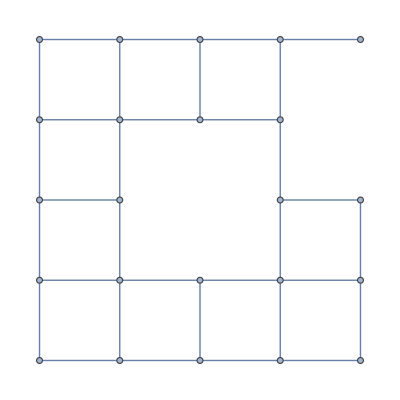

```mathematica
Graph[VertexDelete[GridGraph[{5,5}],13|24],VertexCoordinates ->DeleteCases[bugGraphCoords[[1;;]], x_/;x=={3,3}||x=={5,4}]]
```

```mathematica
DeleteCases[bugGraphCoords[[1;;]], x_/;x=={3.,3.}||x=={5,5}]
```

{{1.,1.},{1.,2.},{1.,3.},{1.,4.},{1.,5.},{2.,1.},{2.,2.},{2.,3.},{2.,4.},{2.,5.},{3.,1.},{3.,2.},{3.,4.},{3.,5.},{4.,1.},{4.,2.},{4.,3.},{4.,4.},{4.,5.},{5.,1.},{5.,2.},{5.,3.},{5.,4.}}

```mathematica
DeleteCases[bugGraphCoords[[1;;]],x_/; !FreeQ[x, Alternatives@@{{3.,3.},{5.,5.}}]]
```

{{1.,1.},{1.,2.},{1.,3.},{1.,4.},{1.,5.},{2.,1.},{2.,2.},{2.,3.},{2.,4.},{2.,5.},{3.,1.},{3.,2.},{3.,4.},{3.,5.},{4.,1.},{4.,2.},{4.,3.},{4.,4.},{4.,5.},{5.,1.},{5.,2.},{5.,3.},{5.,4.}}

```mathematica
Grid[]
```

```mathematica
DeleteCases[baseNodeList[[1;;]],covered];
```

```mathematica
Alternatives@@{{3,3},{5,5}}
```

{3,3}|{5,5}

```mathematica
Alternatives @@ {{3,3},{5,5}}
```

{3,3}|{5,5}

### A-Star

```mathematica
runAStar[graph_]:=
Module[{running = True,embedding = GraphEmbedding[graph]
},
openNodes = {{startNodeCoords},{0}};
closedNodes = {{},{}};

While[Length[openNodes[[1]]] ≠ 0 &&running == True,
Module[{parentNode=Take[openNodes[[1]],Position[openNodes[[2]],Min[openNodes[[2]]]]//Flatten]//Flatten},
openNodes[[1]] = DeleteCases[openNodes[[1]], x_/; x==parentNode];
openNodes[[2]]=DeleteCases[openNodes[[2]], x_/; x==cost[parentNode]];
With[{successorNodes =genSuccsessorNodes[Take[baseNodeList,Position[baseNodeCoordList,parentNode]//Flatten]//Flatten]},
For[i=0,i<Length[successorNodes],i++,
If[successorNodes[[i]]==goalNodeCoords,Print["Found the goal"];running = False;,
With[{currentNodeCost =runningCost[successorNodes[[i]]], parentNode},
If[!FreeQ[openNodes[[2]],currentNodeCost]|| !FreeQ[openNodes[[1]],successorNodes[[i]]],,
If[!FreeQ[closedNodes[[2]],currentNodeCost]|| !FreeQ[closedNodes[[1]],successorNodes[[i]]], ,
openNodes={Append[openNodes[[1]],successorNodes[[i]]], Append[openNodes[[2]], currentNodeCost]};
];
]
]
];
];
closedNodes =Append[closedNodes,{parentNode,cost[parentNode]}];
(*Print[openNodes]*)
]
]
];
If[running == True,Print["No possible solution"];]
]
```

```mathematica
Take[openNodes[[1]],Position[openNodes[[2]],Min[openNodes[[2]]]]//Flatten]//Flatten
```

{1.,1.}

```mathematica
getSuccsessorNodes[Take[baseNodeList,Position[baseNodeCoordList,{1.,1.}]//Flatten]//Flatten]
```

{{2.,1.},{1.,2.}}

```mathematica
Take[openNodes[[1]],Position[openNodes[[2]],Min[openNodes[[2]]]]//Flatten]//Flatten
```

{1.,1.}

```mathematica
Take[baseNodeList,Position[baseNodeCoordList,{1.,1.}]//Flatten]
```

{1}

```mathematica
Take[openNodes[[1]],Position[openNodes[[2]],Min[openNodes[[2]]]]//Flatten]
```

{{1.,1.}}

```mathematica
runningCost[{1,1},{2,2}]
```

(1.41421+Floor[-2.+2. n])^2

```mathematica
genSuccsessorNodes[81]
```

{{10.,1.},{8.,1.},{9.,2.}}

```mathematica
runAStar[graph]
```

With::lvws: Variable parentNode$ in local variable specification {currentNodeCost$=runningCost[{{2.,1.},{1.,2.}}⟦i⟧],parentNode$} requires a value.

No possible solution

### A-Star V2

```mathematica
forReplacementFunc[successorNodes_]:=
```

```mathematica
runAStarV2[graph_]:=
Module[{running = True,embedding = GraphEmbedding[graph]
},
openNodes = {{startNodeCoords},{0}};
closedNodes = {{},{}};

While[Length[openNodes[[1]]] ≠ 0 &&running == True,
Module[{parentNode=Take[openNodes[[1]],Position[openNodes[[2]],Min[openNodes[[2]]]]//Flatten]//Flatten},
openNodes[[1]] = DeleteCases[openNodes[[1]], x_/; x==parentNode];
openNodes[[2]]=DeleteCases[openNodes[[2]], x_/; x==cost[parentNode]];
Module[{successorNodes =genSuccsessorNodes[Take[baseNodeList,Position[baseNodeCoordList,parentNode]//Flatten]//Flatten]},

closedNodes =Append[closedNodes,{parentNode,cost[parentNode]}];
]
]
];
If[running == True,Print["No possible solution"];]
]
```

```mathematica
runAStarV2[graph]
```

No possible solution

## 2D Implementation

### Initialization / Reset

```mathematica
startNodeCoords = {1.,1.};
goalNodeCoords = {10.,10.};

openNodes ={ {startNodeCoords},{0}};
closedNodes = {{},{}};

getCoords[n_]:= GraphEmbedding[baseGraph][[n]]

getSuccsessorNodes[n_]:= With[{nodeCoord=getCoords[n]//Flatten}, DeleteCases[{nodeCoord+{1,0}, nodeCoord-{1,0}, nodeCoord+{0,1}, nodeCoord-{0,1}, nodeCoord+{1,1}, nodeCoord-{1,1}, nodeCoord+{1,-1}, nodeCoord+{-1,1}}, x_/;FreeQ[GraphEmbedding[graph], x]]] (*Diagonal movement allowed*)

runningCost[cn_,pn_]:=Floor[N[(Total[goalNodeCoords-cn]+EuclideanDistance[cn,pn])]+1](*Faster but non-admissable heuristic*)
(*runningCost[cn_,pn_]:=Floor[N[Total[cn-startNodeCoords]]+EuclideanDistance[cn,goalNodeCoords]]*)

baseGraph = GridGraph[{10,10}];
baseNodeList = VertexList[baseGraph];
baseNodeCoordList = GraphEmbedding[baseGraph];
meanPt=Mean[baseNodeCoordList];

diskPosList = Table[{RandomReal[{1,10}],RandomReal[{1,10}]},{x,7}];
(*diskPosList = {{9,9}};*)
getCoveredNodes[diskPosList_]:=Position[baseNodeCoordList, p_/; Norm[p-#]≤ 1& @ diskPosList, {1}]//Flatten;
covered=Alternatives@@((getCoveredNodes /@ diskPosList)//Flatten);

getCoveredNodeCoords[diskPosList_]:= Alternatives@@ Flatten[getCoords/@ getCoveredNodes /@diskPosList,1];
coveredNodeCoords=getCoveredNodeCoords[diskPosList];

coordToNode[n_]:= Floor[(n[[1]]-1)*10 +n[[2]]]

genGraphV3[coveredNodes_]:=
With[{coveredNodeCoords = getCoords /@coveredNodes},Graph[VertexDelete[baseGraph,coveredNodes],VertexCoordinates ->DeleteCases[baseNodeCoordList[[1;;]], x_/;!FreeQ[x,coveredNodeCoords]]]
]
graph = genGraphV3[covered];

makeCoordList[x1_,y1_]:= {x1,y1}

nodeStateConverter[states_]:=Module[{returning = {}},
For[i = 1, i≤ Length[states], If[states[[i]]== 1,returning=Append[returning, baseNodeList[[i]]]];i++];
Return[returning]
]
```

### A* Code

```mathematica
successorTest[n_, pn_, pnCost_]:=With[{nodeCost = runningCost[n,pn]},
If[n==goalNodeCoords, 
Print["Found the goal!"]; running=False;,
If[!FreeQ[openNodes[[1]], n]||!FreeQ[closedNodes[[1]],n],,
If[Min[openNodes[[2]]] < nodeCost ,,
openNodes={Append[openNodes[[1]],n], Append[openNodes[[2]], nodeCost]};
];
];
];
];
```

```mathematica
executeAStar[graph_]:=
Block[{running = True, thisGraph = graph} ,
With[{embedding = GraphEmbedding[thisGraph]},
openNodes ={ {startNodeCoords},{0}};
          closedNodes = {{},{}};

While[Length[openNodes[[1]]] > 0 &&running == True,
With[{parentCost=Part[openNodes[[2]],Part[Position[openNodes[[2]], Min[openNodes[[2]]]]//Flatten,1]]},With[{parentNode=Take[openNodes[[1]],Position[openNodes[[2]], parentCost,1,1]//Flatten]//Flatten},
openNodes[[2]]=Drop[openNodes[[2]],Position[openNodes[[1]], parentNode]//Flatten];
openNodes[[1]] = DeleteCases[openNodes[[1]], x_/; x==parentNode];
With[{successorNodes =getSuccsessorNodes[Take[baseNodeList,Position[baseNodeCoordList,parentNode]//Flatten]//Flatten]},
successorTest[#,parentNode,parentCost]&/@successorNodes;
];
If[parentNode≠ {1.,1.},closedNodes ={Append[closedNodes[[1]],parentNode], Append[closedNodes[[2]], parentCost]}]
];
];
];
If[running==True, Print["No possible solution."]];
];
 Graph[HighlightGraph[HighlightGraph[thisGraph,Append[coordToNode /@ closedNodes[[1]], {coordToNode[goalNodeCoords],coordToNode[startNodeCoords]}]],Style[coordToNode /@ openNodes[[1]],Green]], VertexSize->{coordToNode[goalNodeCoords]-> Medium, coordToNode[startNodeCoords]-> Medium}]
]
```

### Execution and Testing

Found the goal!

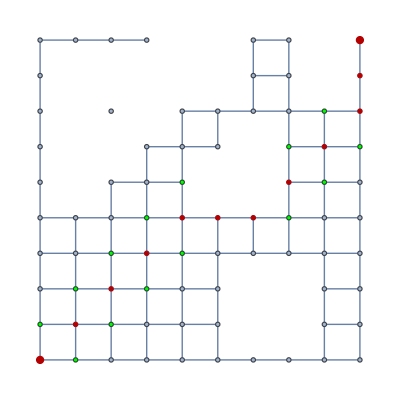

```mathematica
executeAStar[graph]
```

```mathematica
Mean[DeleteCases[Table[
diskPosList = Table[{RandomReal[{1,10}],RandomReal[{1,10}]};,{x,7}];
covered=Alternatives@@((getCoveredNodes /@ diskPosList)//Flatten);
graph = genGraphV3[covered];
AbsoluteTiming[executeAStar[graph]] , {x,1,10000}
]
//Flatten, x_/;x==Null]
]
```

0.00611325

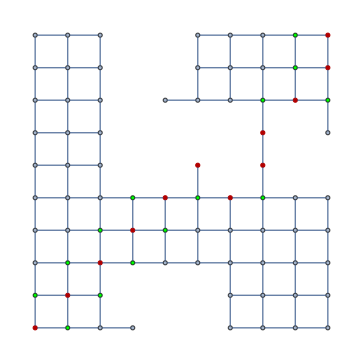
```mathematica
-Graphics-
(*
As seen here, this cost-function/heuristic sometimes sacrifices the optimal path for speed,  however, it is only by a factor of Sqrt[2] edge distance longer for each occurrence
*)
```

```mathematica
openNodes
```

{{{2.,1.},{1.,2.},{3.,2.},{2.,3.},{4.,3.},{3.,4.},{4.,5.},{3.,6.},{6.,3.},{8.,3.},{9.,4.},{10.,5.},{9.,6.},{9.,7.},{9.,9.},{9.,10.}},{19,19,17,17,15,15,13,13,13,11,9,7,7,6,4,3}}

```mathematica
closedNodes
```

{{{2.,2.},{3.,3.},{4.,4.},{5.,5.},{6.,6.},{7.,7.},{8.,8.},{9.,9.}},{18,16,14,12,10,8,6,4}}

### Manipulate

#### Manipulate A* Code

```mathematica
manipSuccessorTest[n_, pn_, pnCost_]:=With[{nodeCost = runningCost[n,pn]},
If[n==goalNodeCoords, 
(*Print["Found the goal!"];*) running=False;,
If[!FreeQ[openNodes[[1]], n]||!FreeQ[closedNodes[[1]],n],,
If[Min[openNodes[[2]]] < nodeCost ,,
openNodes={Append[openNodes[[1]],n], Append[openNodes[[2]], nodeCost]};
];
];
];
];
```

```mathematica
manipExecuteAStar[thisGraph_]:=
Block[{running = True} ,
With[{embedding = GraphEmbedding[thisGraph]},
openNodes ={ {startNodeCoords},{0}};
          closedNodes = {{},{}};

While[Length[openNodes[[1]]] > 0 &&running == True,
With[{parentCost=Part[openNodes[[2]],Part[Position[openNodes[[2]], Min[openNodes[[2]]]]//Flatten,1]]},With[{parentNode=Take[openNodes[[1]],Position[openNodes[[2]], parentCost,1,1]//Flatten]//Flatten},
openNodes[[2]]=Drop[openNodes[[2]],Position[openNodes[[1]], parentNode]//Flatten];
openNodes[[1]] = DeleteCases[openNodes[[1]], x_/; x==parentNode];
With[{successorNodes =getSuccsessorNodes[Take[baseNodeList,Position[baseNodeCoordList,parentNode]//Flatten]//Flatten]},
manipSuccessorTest[#,parentNode,parentCost]&/@successorNodes;
];
If[parentNode≠ {1.,1.},closedNodes ={Append[closedNodes[[1]],parentNode], Append[closedNodes[[2]], parentCost]}]
];
];
]
(*If[running==True, Print["No possible solution."]];*)
];
 Rotate[Graph[HighlightGraph[HighlightGraph[thisGraph,Append[coordToNode /@ closedNodes[[1]], {coordToNode[goalNodeCoords],coordToNode[startNodeCoords]}]],Style[coordToNode /@ openNodes[[1]],Green]], VertexSize->{coordToNode[goalNodeCoords]-> Medium, coordToNode[startNodeCoords]-> Medium}],-90 Degree]
]
```

```mathematica
genGraphV4[coveredNodeStates_, h_, w_]:=
Block[{coveredNodes = nodeStateConverter[coveredNodeStates//Flatten]},
Graph[VertexDelete[GridGraph[{w,h}],coveredNodes],VertexCoordinates ->DeleteCases[GraphEmbedding[GridGraph[{h,w}]][[1;;]], x_/;!FreeQ[getCoords /@ coveredNodes,x]]]
]
```

#### Manipulate Implementation

```mathematica
Manipulate[manipExecuteAStar[graph = genGraphV4[input,10,10]],{{input, Table[RandomInteger[{0,1},10],{x,10}]}, ControlType -> None},Dynamic[Panel[Grid[Outer[Checkbox[Dynamic[input[[#1,#2]]],{1,0}]&,Range[10],Range[10]]]]]]
```

## 3D Implementation *WIP*

### Initialization / Reset

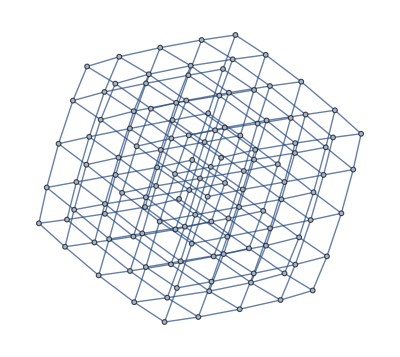

```mathematica
startNodeCoords = {1.,1.};
goalNodeCoords = {10.,10.};

openNodes ={ {startNodeCoords},{0}};
closedNodes = {{},{}};

getCoords[n_]:= GraphEmbedding[baseGraph][[n]]

getSuccsessorNodes[n_]:= With[{nodeCoord=getCoords[n]//Flatten}, DeleteCases[{nodeCoord+{1,0}, nodeCoord-{1,0}, nodeCoord+{0,1}, nodeCoord-{0,1}, nodeCoord+{1,1}, nodeCoord-{1,1}, nodeCoord+{1,-1}, nodeCoord+{-1,1}}, x_/;FreeQ[GraphEmbedding[graph], x]]] (*Diagonal movement allowed*)

runningCost[cn_,pn_]:=Floor[N[(Total[goalNodeCoords-cn]+EuclideanDistance[cn,pn])]+1](*Faster but non-admissable heuristic*)
(*runningCost[cn_,pn_]:=Floor[N[Total[cn-startNodeCoords]]+EuclideanDistance[cn,goalNodeCoords]]*)

base3DGraph = GridGraph[{5,5,5}]
base3DNodeList = VertexList[base3DGraph];
base3DNodeCoordList = GraphEmbedding[base3DGraph];
mean3DPt=Mean[base3DNodeCoordList];

coordToNode3D[n_]:= Floor[(n[[1]]-1)*10 +n[[2]]]

gen3DGraph[coveredNodes_]:=
With[{coveredNodeCoords = getCoords /@coveredNodes},Graph[VertexDelete[baseGraph,coveredNodes],VertexCoordinates ->DeleteCases[baseNodeCoordList[[1;;]], x_/;!FreeQ[x,coveredNodeCoords]]]
]
graph = gen3DGraph[covered];
```

### A* Code

```mathematica
successorTest3D[n_, pn_, pnCost_]:=With[{nodeCost = runningCost[n,pn]},
If[n==goalNodeCoords, 
Print["Found the goal!"]; running=False;,
If[!FreeQ[openNodes[[1]], n]||!FreeQ[closedNodes[[1]],n],,
If[Min[openNodes[[2]]] < nodeCost ,,
openNodes={Append[openNodes[[1]],n], Append[openNodes[[2]], nodeCost]};
];
];
];
];
```

```mathematica
execute3DAStar[graph_]:=
Block[{running = True},
With[{embedding = GraphEmbedding[graph]},
openNodes ={ {startNodeCoords},{0}};
          closedNodes = {{},{}};

While[Length[openNodes[[1]]] > 0 &&running == True,
With[{parentCost=Part[openNodes[[2]],Part[Position[openNodes[[2]], Min[openNodes[[2]]]]//Flatten,1]]},With[{parentNode=Take[openNodes[[1]],Position[openNodes[[2]], parentCost,1,1]//Flatten]//Flatten},
openNodes[[2]]=Drop[openNodes[[2]],Position[openNodes[[1]], parentNode]//Flatten];
openNodes[[1]] = DeleteCases[openNodes[[1]], x_/; x==parentNode];
With[{successorNodes =getSuccsessorNodes[Take[baseNodeList,Position[baseNodeCoordList,parentNode]//Flatten]//Flatten]},
successorTest[#,parentNode,parentCost]&/@successorNodes;
];
If[parentNode≠ {1.,1.},closedNodes ={Append[closedNodes[[1]],parentNode], Append[closedNodes[[2]], parentCost]}]
];
];
];
If[running==True, Print["No possible solution."]];
];
visualGraph = Graph[HighlightGraph[HighlightGraph[graph,Append[coordToNode /@ closedNodes[[1]], {coordToNode[goalNodeCoords],coordToNode[startNodeCoords]}]],Style[coordToNode /@ openNodes[[1]],Green]], VertexSize->{coordToNode[goalNodeCoords]-> Medium, coordToNode[startNodeCoords]-> Medium}]
]
```

### Execution and Testing